## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"}
exportOptions={"AllowRasterization"->True,ImageSize->340,ImageResolution->800};
```

{PerformanceGoal→Quality,PlotRange→Full,FrameLabel→{-Graphics-,-Graphics-},{BaseStyle→Directive[FontSize→12],AxesStyle→Directive[FontSize→12],TicksStyle→Directive[FontSize→12],LabelStyle→{FontFamily→Latin Modern Roman,FontSize→12},BaseStyle→texStyle},ColorFunction→SunsetColors}

## Defining the Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
as={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

# N = 1

```mathematica
nn=1;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{λ,χ},Evaluate@HH,Evaluate@compileOptions]
```

{{-1/2-λ/4,-χ/2},{-χ/2,1/2-λ/4-χ^2}}

CompiledFunction[…]

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-1/2-λ/4 | -χ/2
-χ/2 | 1/2-λ/4-χ^2)

## Energies and eigenvalues

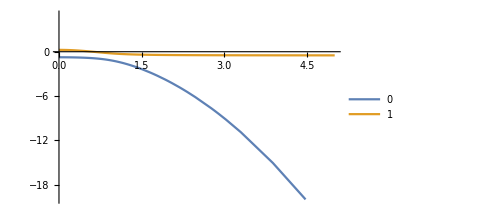
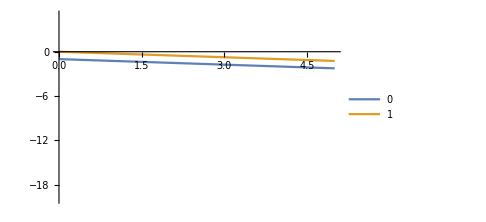

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->Range[0,nn],PlotPoints->10,PlotRange->{Automatic,{-20,5}},Evaluate@font,ImageSize->Medium};
{Plot[energies1,{χ,0,5},Evaluate@plotOpt],
Plot[energies2,{λ,0,5},Evaluate@plotOpt]}
```

## Metric tensor

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
FullSimplify[{{g11,g12},{g12,g22}}]
]
```

```mathematica
g[λ,χ][[2,2]]/.χ->χ[t]
```

((1+χ[t]^2)^2)/(4 (1-χ[t]^2+χ[t]^4)^2)

```mathematica
dsol=DSolve[{((1+χ[τ]^2)^2)/(4 (1-χ[τ]^2+χ[τ]^4)^2)χ'[τ]^2==1,χ[τf]==χf},χ[τ],τ,Assumptions->{χ>0,χi>0,χf>0,τf>0,λ∈Reals}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{χ[τ]→1/2 Cot[2 τ-2 τf-ArcTan[χf/(-1+χf^2)]] (-1+√(1+4 Tan[2 τ-2 τf-ArcTan[χf/(-1+χf^2)]]^2))},{χ[τ]→-1/2 Cot[2 τ-2 τf-ArcTan[χf/(-1+χf^2)]] (1+√(1+4 Tan[2 τ-2 τf-ArcTan[χf/(-1+χf^2)]]^2))},{χ[τ]→-1/2 Cot[2 τ-2 τf+ArcTan[χf/(-1+χf^2)]] (-1+√(1+4 Tan[2 τ-2 τf+ArcTan[χf/(-1+χf^2)]]^2))},{χ[τ]→1/2 Cot[2 τ-2 τf+ArcTan[χf/(-1+χf^2)]] (1+√(1+4 Tan[2 τ-2 τf+ArcTan[χf/(-1+χf^2)]]^2))}}

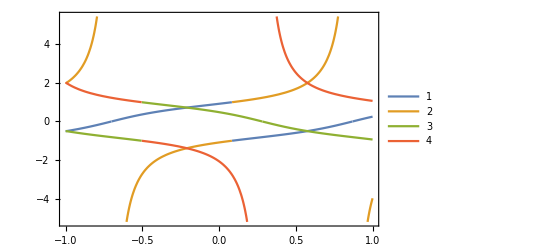

```mathematica
Plot[Evaluate[(χ[τ]/.dsol)/.{χf->2,τf->10}],{τ,-1,1},PlotLegends->Automatic,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"\\tau","\\chi"}]
```

# N = 2

```mathematica
nn=2;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{λ,χ},Evaluate@HH,Evaluate@compileOptions]
```

{{-1-λ/4,-χ/(2 √2),-λ/4},{-χ/(2 √2),1/2 (-λ-χ^2),-1/2 (1/(√2)+√2) χ},{-λ/4,-1/2 (1/(√2)+√2) χ,1+1/2 (-λ/2-4 χ^2)}}

CompiledFunction[…]

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-1-λ/4 | -χ/(2 √2) | -λ/4
-χ/(2 √2) | -λ/2-χ^2/2 | -(3 χ)/(2 √2)
-λ/4 | -(3 χ)/(2 √2) | 1-λ/4-2 χ^2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

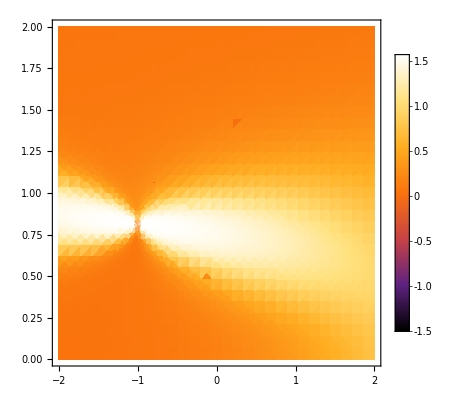

```mathematica
DensityPlot[ArcTan@gC[λ,χ],{λ,-2,2},{χ,0,2},Evaluate@densityPlotOptions,PlotPoints->30]
```

## Energies and eigenvalues

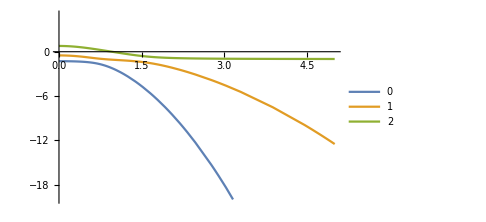
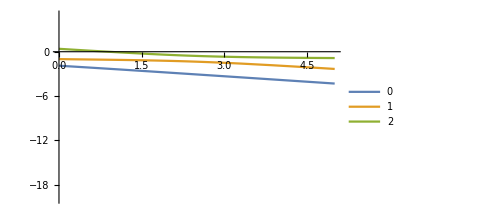

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->Range[0,nn],PlotPoints->10,PlotRange->{Automatic,{-20,5}},Evaluate@font,ImageSize->Medium};
{Plot[energies1,{χ,0,5},Evaluate@plotOpt],
Plot[energies2,{λ,0,5},Evaluate@plotOpt]}
```

Analytical formula for energies Eigenvalues[H[λ,χ],Cubics→True] can be rewritten using some substitution, because of rounding errors (order of numerical precision 10^-16)

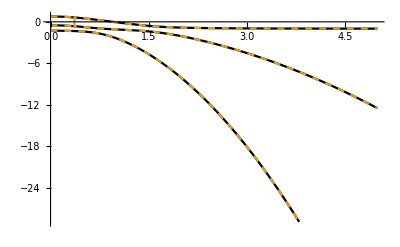

```mathematica
enA[λ_,χ_]:=2^(2/3)(2 λ (18+λ^2)-3 (-48+λ (45+λ)) χ^2+3 (-9+11 λ) χ^4-70 χ^6+√(-4 enD[λ,χ]^3+(2 λ (18+λ^2)-3 (-48+λ (45+λ)) χ^2+3 (-9+11 λ) χ^4-70 χ^6)^2))^(1/3);
enB[λ_,χ_]:=4 (2 λ+5 χ^2);
enD[λ_,χ_]:=(12+λ^2-(9+λ) χ^2+13 χ^4);
enSim[λ_,χ_]:=1/24 { 
(- enB[λ,χ]-(8 (-1)^(1/3) enD[λ,χ])/enA[λ,χ]+(-1+ⅈ √3) enA[λ,χ]), 
(- enB[λ,χ]+(8 (-1)^(2/3) enD[λ,χ])/enA[λ,χ]-(1+ⅈ √3) enA[λ,χ]),
(- enB[λ,χ]+(8enD[λ,χ])/enA[λ,χ]+2  enA[λ,χ])}
Plot[{Re@enSim[1,χ],Eigenvalues[H[1,χ]]},{χ,0,5},PlotStyle->{Black,Dashed}]
```

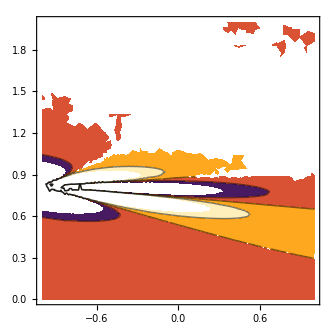

```mathematica
ContourPlot[Evaluate@D[enSim[λ,χ]⟦1⟧,{χ,2},{λ,2}],{λ,-1,1},{χ,0,2},ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->10]
```

```mathematica
dens=DensityPlot[Det@gC[λ,χ],{λ,-1,20},{χ,0,2},ImageSize->Large,ColorFunction->"SunsetColors",PlotPoints->15,ScalingFunctions->"Log"];
```

```mathematica
DenSim1[λ_,χ_]=D[enSim[λ,χ]⟦1⟧-enSim[λ,χ]⟦2⟧,{χ,1},{λ,1}];
```

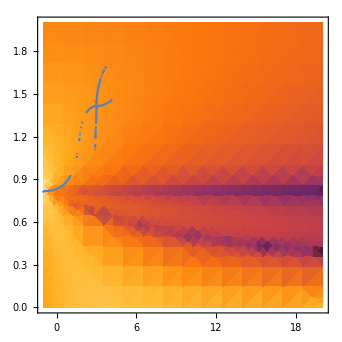

```mathematica
cont=ContourPlot[DenSim1[λ,χ]==0,{λ,-1,20},{χ,0,2},ImageSize->Large,PlotPoints->25];
Show[dens,cont]
```

## Metric tensor

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
g11=Re@Sum[((Conjugate[eigenVec[λ,χ][[1]]].DH1[λ,χ].eigenVec[λ,χ][[i]])(Conjugate[eigenVec[λ,χ][[i]]].DH1[λ,χ].eigenVec[λ,χ][[1]]))/(enSim[λ,χ][[1]]-enSim[λ,χ][[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenVec[λ,χ][[1]]].DH1[λ,χ].eigenVec[λ,χ][[i]]Conjugate[eigenVec[λ,χ][[i]]].DH2[λ,χ].eigenVec[λ,χ][[1]])/(enSim[λ,χ][[1]]-enSim[λ,χ][[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenVec[λ,χ][[1]]].DH2[λ,χ].eigenVec[λ,χ][[i]])(Conjugate[eigenVec[λ,χ][[i]]].DH2[λ,χ].eigenVec[λ,χ][[1]]))/(enSim[λ,χ][[1]]-enSim[λ,χ][[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
N@g[3,5]
N@g[-1,-1]
```

{{0.0000273694,-0.0000780008},{-0.0000780008,0.000997044}}

{{0.12963,0.0555556},{0.0555556,0.222222}}

# N = 3

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2+1/3 (-(7 λ)/4-χ^2),-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/2+1/3 (-(7 λ)/4-4 χ^2),-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2+1/3 (-(3 λ)/4-9 χ^2)}}

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(1/4 (-6-λ) | -χ/(2 √3) | -λ/(2 √3) | 0
-χ/(2 √3) | 1/12 (-6-7 λ-4 χ^2) | -χ | -λ/(2 √3)
-λ/(2 √3) | -χ | 1/12 (6-7 λ-16 χ^2) | -(5 χ)/(2 √3)
0 | -λ/(2 √3) | -(5 χ)/(2 √3) | 3/2-λ/4-3 χ^2)

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Energies and eigenvalues

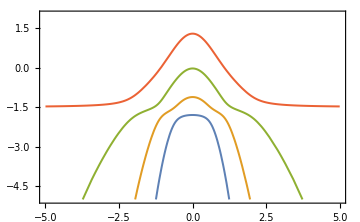
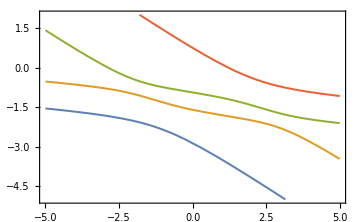

```mathematica
energies1=Eigenvalues[H[1,χ]];
energies2=Eigenvalues[H[λ,1]];
plotOpt={PlotLegends->MaTeX/@{"E_0","E_1","E_2","E_3"},PlotPoints->20,PlotRange->{Automatic,{-5,2}},Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->Thickness[0.004]};
{plA,plB}={Plot[energies1,{χ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\chi","Energy"}],
Plot[energies2,{λ,-5,5},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","Energy"}]}
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_energiesl.pdf",plA,"AllowRasterization"->True,ImageSize->340,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_energiesc.pdf",plB,"AllowRasterization"->True,ImageSize->340,ImageResolution->800];
```

Analytical formula for energies Eigenvalues[H[λ,χ],Cubics→True] can be rewritten using some substitution, because of rounding errors (order of numerical precision 10^-16)

```mathematica
en[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
```

```mathematica
points=
enDifPlot=Show[{
DensityPlot[(#⟦4⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-0.55,-0.45},{χ,0.7,0.9},Evaluate@densityPlotOptions,PlotPoints->150, ImageSize->310],
ListPlot[{{-1/2,Sqrt[3/5]},{-1/2,-Sqrt[3/5]}},PlotStyle->Green]
}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_en4-en1.pdf",enDifPlot,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
FindMinimum[Flatten@{(#⟦4⟧-#⟦1⟧)&/@{en[λ,χ]},-1<λ<0,0<χ<1},{λ,-0.55},{χ,0.5}]
```

{0.744182,{λ→-4.46254×10^-8,χ→1.}}

```mathematica
NMinimize[{(#⟦4⟧-#⟦1⟧)&/@{en[λ,χ]},-1<λ<0,0<χ<1},{λ,χ}]
```

NMinimize[{{-λ+en[λ,χ]⟦4⟧},-1<λ<0,0<χ<1},{λ,χ}]

```mathematica
enDifPlotd=DensityPlot[(#⟦4⟧-#⟦1⟧)&/@{ND[en[λ,c],c,χ]},{λ,-5,5},{χ,-1.2,1.2},Evaluate@densityPlotOptions,PlotPoints->150, ImageSize->310]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_en4-en1_der.pdf",enDifPlotd,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Eigenvalues[H[λ,χ],Quartics->True]
```

```mathematica
enA[λ_,χ_]:=16 2^(1/3) (25515+64 λ^6-108621 χ^2-192 λ^5 χ^2+309096 χ^4-326727 χ^6+162648 χ^8-81855 χ^10+24013 χ^12-8 λ^3 χ^2 (-513+414 χ^2+29 χ^4)+24 λ^4 (36-93 χ^2+52 χ^4)+6 λ χ^2 (16119-42660 χ^2+29691 χ^4-3198 χ^6+409 χ^8)+6 λ^2 (1377-10557 χ^2+17595 χ^4-10053 χ^6+1225 χ^8)+√(-(1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)^3+(25515+8262 λ^2+864 λ^4+64 λ^6-3 (36207+2 λ (-16119+λ (10557+4 λ (-171+λ (93+8 λ))))) χ^2+6 (51516+λ (-42660+λ (17595+8 λ (-69+26 λ)))) χ^4-(326727+2 λ (-89073+λ (30159+116 λ))) χ^6+6 (27108+λ (-3198+1225 λ)) χ^8+3 (-27285+818 λ) χ^10+24013 χ^12)^2))^(1/3)
enC[λ_,χ_]:=(256 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8))/(3 enA[λ,χ])
enB[λ_,χ_]:=4 √(16/3 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4)+enC[λ,χ]+1/(3 2^(1/3))enA[λ,χ])
enD[λ_,χ_]:=8 (5 λ+14 χ^2)^2-8/3 (-180+59 λ^2+132 χ^2+436 λ χ^2+392 χ^4)-enC[λ,χ]-1/(3 2^(1/3))enA[λ,χ]
enE[λ_,χ_]:=(9216 (λ-4 (-1+λ) χ^2+(-1+λ) χ^4-2 χ^6))/enB[λ,χ]
enF[λ_,χ_]:=1/2 √(16/3 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4)+enC[λ,χ]+1/(3 2^(1/3))enA[λ,χ])
enG[λ_,χ_]:=-5 λ-14 χ^2
```

```mathematica
enSim[λ_,χ_]:=
{1/12 (enG[λ,χ]-enF[λ,χ]-1/2 √(enD[λ,χ]-enE[λ,χ])),
1/12 (enG[λ,χ]-enF[λ,χ]+1/2 √(enD[λ,χ]-enE[λ,χ])),
1/12 (enG[λ,χ]+enF[λ,χ]-1/2 √(enD[λ,χ]+enE[λ,χ])),
1/12 (enG[λ,χ]+enF[λ,χ]+1/2 √(enD[λ,χ]+enE[λ,χ]))}
```

```mathematica
N@enSim[-2,14]
N@Eigenvalues[H[-2,14]]
```

{-587.247-2.32905×10^-15 ⅈ,-259.428+1.37007×10^-14 ⅈ,-63.9224-3.44736×10^-14 ⅈ,-0.736116+2.31019×10^-14 ⅈ}

{-587.247,-259.428,-63.9224,-0.736116}

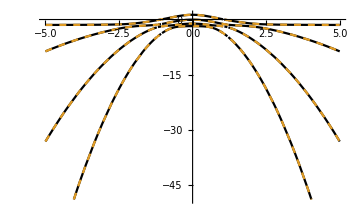
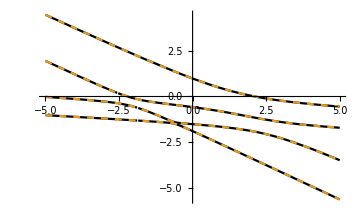

```mathematica
enCompare={PlotStyle->{Black,Dashed},ImageSize->Medium,PlotPoints->10};
{Plot[{Re@enSim[1,χ],Sort@Eigenvalues[H[1,χ]]},{χ,-5,5},Evaluate@enCompare],Plot[{Re@enSim[λ,0.8],Sort@Eigenvalues[H[λ,0.8]]},{λ,-5,5},Evaluate@enCompare]}
```

### Divergence

Crossing E_0 with E_1 for 1/2 √(enD[λ,χ]-enE[λ,χ])=0

```mathematica
FindInstance[enD[λ,χ]==enE[λ,χ],{λ,χ},Reals]
```

{{λ→-1/2,χ→√(3/5)}}

```mathematica
FindInstance[enD[λ,χ]==enE[λ,χ],{λ,χ}]
```

$Aborted

### Phase transitions

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

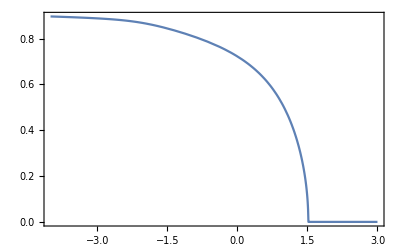

```mathematica
Plot[χ/.Last@FindMaximum[enSim[λ,χ]⟦1⟧-enSim[λ,χ]⟦2⟧,{χ,1}],{λ,-4,3},Evaluate@font,PlotPoints->30,Frame->True]
```

## Eigenvectors

```mathematica
Eigenvectors[H[λ,χ],Quartics->True]
```

```mathematica
eigA[λ_,χ_]:=16 2^(1/3) (25515+64 λ^6-108621 χ^2-192 λ^5 χ^2+309096 χ^4-326727 χ^6+162648 χ^8-81855 χ^10+24013 χ^12-8 λ^3 χ^2 (-513+414 χ^2+29 χ^4)+24 λ^4 (36-93 χ^2+52 χ^4)+6 λ χ^2 (16119-42660 χ^2+29691 χ^4-3198 χ^6+409 χ^8)+6 λ^2 (1377-10557 χ^2+17595 χ^4-10053 χ^6+1225 χ^8)+√(-(1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)^3+(25515+8262 λ^2+864 λ^4+64 λ^6-3 (36207+2 λ (-16119+λ (10557+4 λ (-171+λ (93+8 λ))))) χ^2+6 (51516+λ (-42660+λ (17595+8 λ (-69+26 λ)))) χ^4-(326727+2 λ (-89073+λ (30159+116 λ))) χ^6+6 (27108+λ (-3198+1225 λ)) χ^8+3 (-27285+818 λ) χ^10+24013 χ^12)^2))^(1/3)
eigB[λ_,χ_]:=1/(√6)(√(2^(2/3) eigA[λ,χ]+32 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4)+1/eigA[λ,χ] 512 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)))
eigC[λ_,χ_]:=1/(√6)(√(-2^(2/3) eigA[λ,χ]-1/eigA[λ,χ] 512 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)+64 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4-(216 (λ-4 (-1+λ) χ^2+(-1+λ) χ^4-2 χ^6))/eigB[λ,χ])))
eigD[λ_,χ_]:=1/(√6)(√(-2^(2/3) eigA[λ,χ]-1/eigA[λ,χ] 512 2^(1/3) (1053+144 λ^2+16 λ^4-2 (1161+2 λ (-207+λ (93+8 λ))) χ^2+3 (1329+4 λ (-77+16 λ)) χ^4+2 (-1185+74 λ) χ^6+889 χ^8)+64 (45+4 λ^2-(33+4 λ) χ^2+49 χ^4+(216 (λ-4 (-1+λ) χ^2+(-1+λ) χ^4-2 χ^6))/eigB[λ,χ])))
eigE[λ_,χ_]:=(9+2 λ (9+2 λ)+57 χ^2-22 λ χ^2+49 χ^4)
eigF[λ_,χ_]:=(-81-9 λ+4 λ^3-3 (-54+λ (53+4 λ)) χ^2+3 (-74+13 λ) χ^4+55 χ^6)
```

eigC, eigD differ only in the sign at the end, assign new symbol with \pm

```mathematica
eigenVec[λ_,χ_]:={{((eigB [λ,χ])^3+(eigC [λ,χ])^3-4 (eigC [λ,χ])^2 (-9+λ+7 χ^2)-16 eigC [λ,χ] eigE[λ,χ]+64 eigF[λ,χ]+(eigB [λ,χ])^2 (3 eigC [λ,χ]-4 (-9+λ+7 χ^2))+eigB [λ,χ] (3 (eigC [λ,χ])^2-8 eigC [λ,χ] (-9+λ+7 χ^2)-16 eigE[λ,χ]))/(288 ((-8+eigB [λ,χ]+eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),(432+48 eigB [λ,χ]+(eigB [λ,χ])^2+48 eigC [λ,χ]+2 eigB [λ,χ] eigC [λ,χ]+(eigC [λ,χ])^2+768 λ+24 eigB [λ,χ] λ+24 eigC [λ,χ] λ+320 λ^2-16 (3 (39+eigB [λ,χ]+eigC [λ,χ])+56 λ) χ^2+176 χ^4)/(24 √3 ((-8+eigB [λ,χ]+eigC [λ,χ]) λ+4 (5+4 λ) χ^2)),(λ (-432+(eigB [λ,χ])^2+24 eigC [λ,χ]+(eigC [λ,χ])^2+2 eigB [λ,χ] (12+eigC [λ,χ])-64 λ (3+λ))+8 (3 (36+eigB [λ,χ]+eigC [λ,χ])-3 (-66+eigB [λ,χ]+eigC [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 ((-8+eigB [λ,χ]+eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1},{((eigB [λ,χ])^3-(eigC [λ,χ])^3-4 (eigC [λ,χ])^2 (-9+λ+7 χ^2)+16 eigC [λ,χ] eigE[λ,χ]+64 eigF[λ,χ]-(eigB [λ,χ])^2 (3 eigC [λ,χ]+4 (-9+λ+7 χ^2))+eigB [λ,χ] (3 (eigC [λ,χ])^2+8 eigC [λ,χ] (-9+λ+7 χ^2)-16 eigE[λ,χ]))/(288 ((-8+eigB [λ,χ]-eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),((eigB [λ,χ])^2+(eigC [λ,χ])^2-24 eigC [λ,χ] (2+λ-2 χ^2)+16 (27+48 λ+20 λ^2-(117+56 λ) χ^2+11 χ^4)-2 eigB [λ,χ] (eigC [λ,χ]-12 (2+λ-2 χ^2)))/(24 √3 ((-8+eigB [λ,χ]-eigC [λ,χ]) λ+4 (5+4 λ) χ^2)),(λ (eigB [λ,χ] (24+eigB [λ,χ])-2 eigB [λ,χ] eigC [λ,χ]+(eigC [λ,χ])^2-8 (54+3 eigC [λ,χ]+8 λ (3+λ)))+8 (3 (36+eigB [λ,χ]-eigC [λ,χ])+3 (66-eigB [λ,χ]+eigC [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 ((-8+eigB [λ,χ]-eigC [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1},{(-(eigB [λ,χ])^3+(eigD [λ,χ])^3-4 (eigD [λ,χ])^2 (-9+λ+7 χ^2)-16 eigD [λ,χ] eigE[λ,χ]+64 eigF[λ,χ]+(eigB [λ,χ])^2 (3 eigD [λ,χ]-4 (-9+λ+7 χ^2))+eigB [λ,χ] (-3 (eigD [λ,χ])^2+8 eigD [λ,χ] (-9+λ+7 χ^2)+16 eigE[λ,χ]))/(288 ((-8-eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3)),((eigB [λ,χ])^2+(eigD [λ,χ])^2+24 eigD [λ,χ] (2+λ-2 χ^2)+16 (27+48 λ+20 λ^2-(117+56 λ) χ^2+11 χ^4)-2 eigB [λ,χ] (eigD [λ,χ]+12 (2+λ-2 χ^2)))/(24 √3 ((-8-eigB [λ,χ]+eigD [λ,χ]) λ+4 (5+4 λ) χ^2)),(λ (-432+(eigB [λ,χ])^2+24 eigD [λ,χ]+(eigD [λ,χ])^2-2 eigB [λ,χ] (12+eigD [λ,χ])-64 λ (3+λ))+8 (3 (36-eigB [λ,χ]+eigD [λ,χ])+3 (66+eigB [λ,χ]-eigD [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 ((-8-eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1},{-(((eigB [λ,χ])^3+(eigD [λ,χ])^3+4 (eigD [λ,χ])^2 (-9+λ+7 χ^2)-16 eigD [λ,χ] eigE[λ,χ]-64 eigF[λ,χ]+(eigB [λ,χ])^2 (3 eigD [λ,χ]+4 (-9+λ+7 χ^2))+eigB [λ,χ] (3 (eigD [λ,χ])^2+8 eigD [λ,χ] (-9+λ+7 χ^2)-16 eigE[λ,χ]))/(288 (-(8+eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3))),-(((eigB [λ,χ])^2+(eigD [λ,χ])^2-24 eigD [λ,χ] (2+λ-2 χ^2)+16 (27+48 λ+20 λ^2-(117+56 λ) χ^2+11 χ^4)+2 eigB [λ,χ] (eigD [λ,χ]-12 (2+λ-2 χ^2)))/(24 √3 ((8+eigB [λ,χ]+eigD [λ,χ]) λ-4 (5+4 λ) χ^2))),(λ ((eigB [λ,χ])^2+2 eigB [λ,χ] (-12+eigD [λ,χ])+(eigD [λ,χ])^2-8 (54+3 eigD [λ,χ]+8 λ (3+λ)))+8 (-3 (-36+eigB [λ,χ]+eigD [λ,χ])+3 (66+eigB [λ,χ]+eigD [λ,χ]) λ+32 λ^2) χ^2-176 (6+5 λ) χ^4)/(24 √3 (-(8+eigB [λ,χ]+eigD [λ,χ]) λ χ+4 (5+4 λ) χ^3)),1}}
```

```mathematica
N@eigenVec[1,1]//TableForm
N@Eigenvectors[H[1,1]]//TableForm
```

0.291934+5.8101×10^-17 ⅈ | 0.694333+7.35711×10^-18 ⅈ | 1.06954+6.036×10^-18 ⅈ | 1.
-2.48418+1.80237×10^-16 ⅈ | -0.659472-7.79491×10^-17 ⅈ | 0.171205-3.46316×10^-17 ⅈ | 1.
0.838122-6.91709×10^-16 ⅈ | -1.66268+1.88354×10^-16 ⅈ | -0.0843572+1.72713×10^-17 ⅈ | 1.
0.109682+3.21229×10^-16 ⅈ | 0.729718-7.00792×10^-17 ⅈ | -1.43865+1.78784×10^-18 ⅈ | 1.

0.291934 | 0.694333 | 1.06954 | 1.
-2.48418 | -0.659472 | 0.171205 | 1.
0.838122 | -1.66268 | -0.0843572 | 1.
0.109682 | 0.729718 | -1.43865 | 1.

## Metric tensor

```mathematica
gC[-1/2,√(3/5)]
```

{{1.06968×10^30,-5.85402×10^29},{-5.85402×10^29,3.20372×10^29}}

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ],Quartics->True];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
densA=DensityPlot[Det@gC[λ,χ],{λ,-3,8},{χ,-1.5,1.5},PlotPoints->300,PerformanceGoal->"Quality", ImageSize->310,Evaluate@densityPlotOptions,ScalingFunctions->"Log10"]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_gDivergence.pdf",densA,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
g11A=DensityPlot[ArcTan@gC[λ,χ]⟦1,1⟧,{λ,-3,8},{χ,-1.5,1.5},PlotPoints->300, Evaluate@densityPlotOptionsExport,ImageSize->190]
g12A=DensityPlot[ArcTan@gC[λ,χ]⟦1,2⟧,{λ,-3,8},{χ,-1.5,1.5},PlotPoints->300,Evaluate@densityPlotOptionsExport,ImageSize->190]
g22A=DensityPlot[ArcTan@gC[λ,χ]⟦2,2⟧,{λ,-3,8},{χ,-1.5,1.5},PlotPoints->300,Evaluate@densityPlotOptionsExport,ImageSize->190]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_g11.pdf",g11A,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_g12.pdf",g12A,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_g22.pdf",g22A,"AllowRasterization"->True,ImageResolution->800];
```

## Geodesics

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
Plot3D[derPiece[λ,χ],{λ,-6,6},{χ,-3,3},PlotLegends->Automatic,PlotPoints->30,PlotRange->All,ColorFunction->"SunsetColors"]
```

CompiledFunction[…]

-Graphics3D-

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
{gammasDen111,gammasDen121,gammasDen122}=DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-3,8},{χ,-1.5,1.5},ImageSize->190,PlotPoints->300,Evaluate@densityPlotOptionsExport]&/@{1,2,3}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{gammasDen211,gammasDen221,gammasDen222}=DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-3,8},{χ,-1.5,1.5},ImageSize->190,PlotPoints->300,Evaluate@densityPlotOptionsExport]&/@{1,2,3}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
barA=BarLegend[{"SunsetColors",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->500]
Export[NotebookDirectory[]<>"../dp_text/img/N=3_barA.pdf",barA,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_G111.pdf",gammasDen111,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_G121.pdf",gammasDen121,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_G122.pdf",gammasDen122,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=3_G211.pdf",gammasDen211,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_G221.pdf",gammasDen221,"AllowRasterization"->True,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=3_G222.pdf",gammasDen222,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-3,4},{χ,-2,2},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->30]
```

-Graphics-

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

### Boundary value problem

```mathematica
tmax=500;
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
sol=NDSolve[Join[eq,dirichlet[0,0,1.2,0.6]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

```mathematica
solM=Quiet@Table[NDSolve[Join[eq,dirichlet[li,xi,-1/2,√(3/5)]],{λ,χ},{t,0,tmax},PrecisionGoal->4,AccuracyGoal->4,Method->"ExplicitRungeKutta",WorkingPrecision->150],{li,-3,4,0.5},{xi,-2,2,0.5}]
```

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.sol,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

-Graphics-

```mathematica
accuracy goal=4, WorkingPrecision=150,init=(li,xi,-1/2,√(3/5))  
-Graphics-
```

### Initial value problem

WorkingPrecision = 70 houd be enough (50 was same as 150)

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
solM2=NDSolve[Join[eq,cauchy[0,0,Cos[π/5.4],Sin[π/5.4]]],{λ,χ},{t,0,5},PrecisionGoal->2,AccuracyGoal->2]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM2,{t,0,5},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

-Graphics-

```mathematica
solMulti1=Quiet@Table[NDSolve[Join[eq,cauchy[-1,i,0.1,0]],{λ,χ},{t,0,10},PrecisionGoal->5,AccuracyGoal->5,WorkingPrecision->170],{i,0.72,0.85,0.01}];
```

```mathematica
accuracy goal=3, WorkingPrecision=70,init=(-1,√(3/5),i,0) for {i,0.01,0.055,0.005}
-Graphics-
```

```mathematica
accuracy goal=5, WorkingPrecision=170,init=(-1,i,0.1,0)
-Graphics-
```

```mathematica
accuracy goal=3, WorkingPrecision=70,init=(-1,i,0.1,0)
-Graphics-
```

## GRQuick

```mathematica
Metin[g[λ,χ],{λ,χ}]
```

```mathematica
DensityPlot[ArcTan@Christoffel[{{0},{0,1}}],{λ,-0.2,0.4},{χ,0,1},Evaluate@densityPlotOptions,PlotPoints->20]
```

```mathematica
Einstein[0,0];
Setlight[1];
geo=Geodesics[t]
```

## Some statistics

### Density

```mathematica
rho[λ_,χ_,β_]:=#/Tr[#]&/@Exp[-β H[λ,χ]]
```

```mathematica
Quiet@DensityPlot[Det@rho[λ,χ,1],{λ,-30,30},{χ,-15,15},Evaluate@densityPlotOptions,PlotPoints->10,ScalingFunctions->"Log"]
```

-Graphics-

### Gibbs free energy

```mathematica
G[λ_,χ_,β_]=-1/β Log[Tr[Exp[-β H[λ,χ]]]]//FullSimplify
```

-Log[ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))]/β

```mathematica
DensityPlot[Evaluate@D[G[λ,χ,8],{χ,2}],{λ,-5,10},{χ,-2,2},Evaluate@densityPlotOptions,PlotPoints->100]
```

-Graphics-

```mathematica
Reduce[D[G[λ,χ,1],{χ,3}]==0,{χ},Reals]
```

$Aborted

```mathematica
ListPlot[{#,χ}/.Last@FindMaximum[D[G[#,χ,1],{χ,2}],{χ,1}]&/@Range[-5,10,0.1]]
```

-Graphics-

```mathematica
DensityPlot[Evaluate@D[G[λ,χ,0.4],{λ,1}],{λ,-30,30},{χ,-4,4},Evaluate@densityPlotOptions,PlotPoints->100]
```

-Graphics-

### Internal energy

```mathematica
U[λ_,χ_,β_]=G[λ,χ,β]+β D[G[λ,χ,β],β]//FullSimplify
```

-(ⅇ^(1/4 β (-6+λ)) (3 ⅇ^(3 β) (6+λ)+ⅇ^(1/3 β (6+λ+χ^2)) (6+7 λ+4 χ^2)+3 ⅇ^(3 β χ^2) (-6+λ+12 χ^2)+ⅇ^(1/3 β (3+λ+4 χ^2)) (-6+7 λ+16 χ^2)))/(12 (ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))))

```mathematica
DensityPlot[U[λ,χ,0.1],{λ,-100,150},{χ,-4,4},Evaluate@densityPlotOptions]
```

### Heat capacity

```mathematica
c[λ_,χ_,β_]=-β D[U[λ,χ,β],β]//FullSimplify
```

(ⅇ^(1/4 β (-6+λ)) β ((ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))) (-6+λ) (3 ⅇ^(3 β) (6+λ)+ⅇ^(1/3 β (6+λ+χ^2)) (6+7 λ+4 χ^2)+3 ⅇ^(3 β χ^2) (-6+λ+12 χ^2)+ⅇ^(1/3 β (3+λ+4 χ^2)) (-6+7 λ+16 χ^2))-1/3 ⅇ^(1/4 β (-6+λ)) (3 ⅇ^(3 β) (6+λ)+ⅇ^(1/3 β (6+λ+χ^2)) (6+7 λ+4 χ^2)+3 ⅇ^(3 β χ^2) (-6+λ+12 χ^2)+ⅇ^(1/3 β (3+λ+4 χ^2)) (-6+7 λ+16 χ^2))^2+4 (ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2))) (9 ⅇ^(3 β) (6+λ)+1/3 ⅇ^(1/3 β (6+λ+χ^2)) (6+λ+χ^2) (6+7 λ+4 χ^2)+9 ⅇ^(3 β χ^2) χ^2 (-6+λ+12 χ^2)+1/3 ⅇ^(1/3 β (3+λ+4 χ^2)) (3+λ+4 χ^2) (-6+7 λ+16 χ^2))))/(48 (ⅇ^(1/4 β (6+λ))+ⅇ^(1/12 β (6+7 λ+4 χ^2))+ⅇ^(1/4 β (-6+λ+12 χ^2))+ⅇ^(1/12 β (-6+7 λ+16 χ^2)))^2)

```mathematica
DensityPlot[c[λ,χ,0.1],{λ,-100,150},{χ,-4,4},Evaluate@densityPlotOptions, PlotLabel->"k_B C"]
```

-Graphics-